```mathematica
SetDirectory[NotebookDirectory[]];
```

## sigma phase boundary

```mathematica
l=60;
fpiall=Table[Flatten[Import["./Tem"<>ToString[i]<>"/buffer/fpi.dat"]],{i,1,l}];
Tc=Table[Max[Table[If[1/fpiall[[j]][[i]]<1&&1/fpiall[[j]][[i+1]]>100,i,0],{i,1,Length[fpiall[[j]]]}]],{j,4,l}];
mub=Flatten[Table[i*11,{i,1,l}]]
```

Part::partw: {81.740043233355224483065292547055076,81.736978812013052723424508805538136,81.731859808182749859237304865840567,«46»,77.26530340177012039274313103260298,«2»} 的部分 53 不存在.

Part::partw: {81.740043233355224483065292547055076,81.736978812013052723424508805538136,81.731859808182749859237304865840567,«46»,76.992453945074212074045971680445374,«1»} 的部分 52 不存在.

Part::partw: {81.740043233355224483065292547055076,81.736978812013052723424505287116193,«34»,77.235013258008962934808067533100927} 的部分 38 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

{11,22,33,44,55,66,77,88,99,110,121,132,143,154,165,176,187,198,209,220,231,242,253,264,275,286,297,308,319,330,341,352,363,374,385,396,407,418,429,440,451,462,473,484,495,506,517,528,539,550,561,572,583,594,605,616,627,638,649,660}

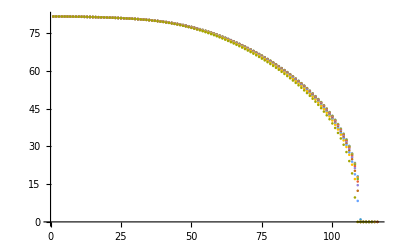

```mathematica
ListPlot[fpiall]
```

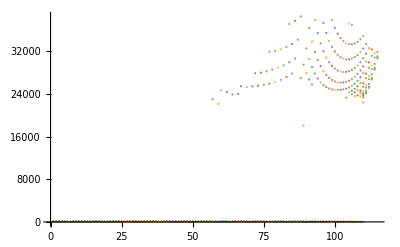

```mathematica
ListPlot[1/fpiall,PlotRange->All]
```

```mathematica
mub2=Flatten[{mub,680,685,700}]
```

{14,28,42,56,70,84,98,112,126,140,154,168,182,196,210,224,238,252,266,280,294,308,322,336,350,364,378,392,406,420,434,448,462,476,490,504,518,532,546,560,574,588,602,616,630,644,658,672,680,685,700}

```mathematica
Length[Tc2]
```

51

```mathematica
Tc2=Flatten[{Tc,73.02,70.873,69.465,64.8267100}];
```

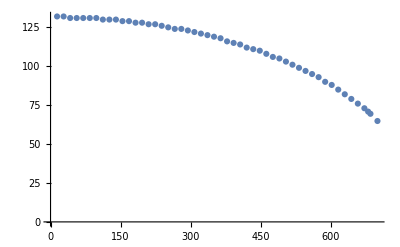

```mathematica
ListPlot[Transpose[{mub2,Tc2}],PlotRange->All]
```

```mathematica
fitpd=FindFit[Transpose[{mub2,Tc2}],a+b x^2+c x^4,{a,b,c},x]
```

{a→131.411,b→-0.0000900599,c→-8.7851×10^-11}

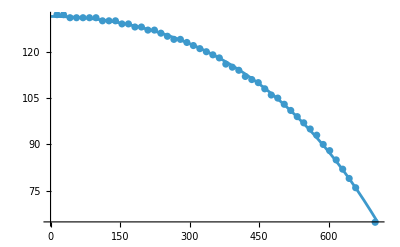

```mathematica
Show[Plot[a+b x^2+c x^4/.fitpd,{x,0,705}],ListPlot[Transpose[{mub2,Tc2}]]]
```

```mathematica
mub={0,50,100,150,200,250,300,350,400,450,500,550,575,600,625,650,675,700};
phaseboundary=Table[{mub[[i]],a+b mub[[i]]^2+c mub[[i]]^4/.fitpd},{i,1,Length[mub]}];
```

```mathematica
Export["pb.dat",phaseboundary]
```

pb.dat

```mathematica
mub={0,50,100,150,200,250,300,350,400,450,500,550,600,650,700};
phaseboundary=Table[{mub[[i]],a+b mub[[i]]^2+c mub[[i]]^4/.fitpd},{i,1,Length[mub]}];
Export["pb2.dat",phaseboundary]
```

pb2.dat